# The P&M Social Network

## March 2017

## Data import

```mathematica
dataset=SemanticImport["/Users/cwoodard/GitHub/PaM2017/graphs/pm-teams-mar2017.csv"]
```

Dataset[<>]

## Graph construction

First, let’s group the data by teams for each experiment:

```mathematica
exp0=dataset[GroupBy["Exp0"]]
```

Dataset[<>]

```mathematica
exp1=dataset[GroupBy["Exp1"]];
exp2=dataset[GroupBy["Exp2"]];
exp3=dataset[GroupBy["Exp3"]];
```

Now let’s extract the node IDs:

```mathematica
exp0Nodes=Normal@Values[exp0[All,All,"Node"]]
```

{{1,29,52,63},{2,30,32,38},{3,23,34,48},{4,39,54,83},{5,6,77,82},{7,10,18,71},{8,25,27,62},{9,26,42,46},{11,24,59,78},{12,33,36,51},{13,40,47,69},{14,37,74,80},{15,45,66,79},{16,35,64,72},{17,28,44},{19,43,49,57},{20,41,53,81},{21,50,65,76},{22,55,58,73},{31,56,60,75},{61,67,68,70}}

```mathematica
exp1Nodes=Normal@Values[exp1[All,All,"Node"]];
exp2Nodes=Normal@Values[exp2[All,All,"Node"]];
exp3Nodes=Normal@Values[exp3[All,All,"Node"]];
```

Okay, now we need some functions or things are going to get really messy:

```mathematica
completeGraphRawPairs[n_]:=Flatten[Table[{i,j+1},{i,1,n-1},{j,i,n-1}],1]
completeGraphMappedPairs[nodes_List]:=Part[nodes,#]&/@completeGraphRawPairs[Length[nodes]]
completeGraphEdges[nodes_List]:=UndirectedEdge[#[[1]],#[[2]]]&/@completeGraphMappedPairs[nodes]
```

Voilà! Our first graph:

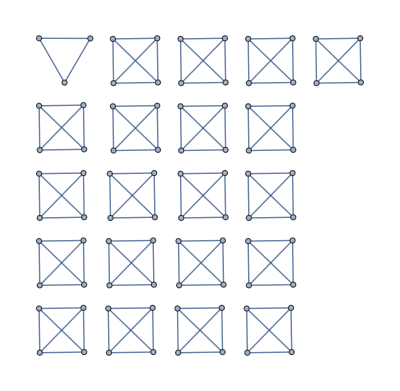

```mathematica
graph0=Graph@Flatten[completeGraphEdges/@exp0Nodes]
```

```mathematica
graph1=Graph@Flatten[completeGraphEdges/@exp1Nodes];
graph2=Graph@Flatten[completeGraphEdges/@exp2Nodes];
graph3=Graph@Flatten[completeGraphEdges/@exp3Nodes];
```

Finally, we string them together:

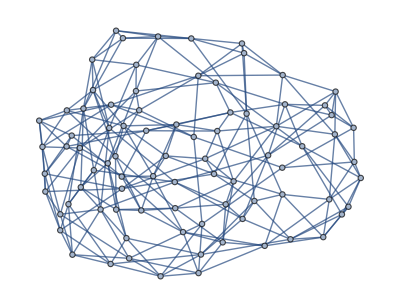

```mathematica
graph01=GraphUnion[graph0,graph1]
```

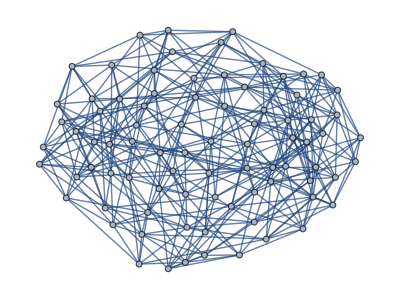

```mathematica
graph012=GraphUnion[graph01,graph2]
```

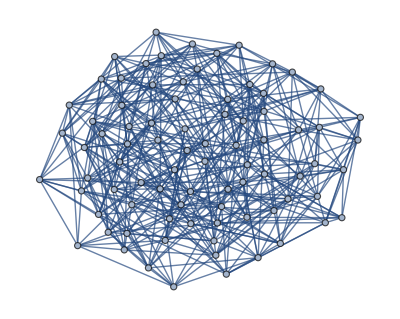

```mathematica
graph0123=GraphUnion[graph012,graph3]
```

And here’s an animation, just for fun:

```mathematica
gl0=Labeled[graph0,"After Experiment 0"];
gl01=Labeled[graph01,"After Experiment 1"];
gl012=Labeled[graph012,"After Experiment 2"];
gl0123=Labeled[graph0123,"After Experiment 3"];
```

```mathematica
graphSequence={graph0,graph01,graph012,graph0123};
labeledGraphSequence={gl0,gl01,gl012,gl0123};
```

```mathematica
anim=Animate[Part[labeledGraphSequence,i],{i,1,4,1},SaveDefinitions->True,AnimationRunning->False]
```

Which we can deploy to the cloud …

```mathematica
CloudDeploy[anim,Permissions->"Public"]
```

CloudObject[]

## Graph analysis

And here is some rudimentary graph analysis:

```mathematica
ConnectedGraphQ[graph0]
```

False

```mathematica
ConnectedGraphQ[graph01]
```

True

```mathematica
VertexCount/@graphSequence
```

{83,83,83,83}

```mathematica
meanGraphDistances=MeanGraphDistance/@graphSequence//N
```

{∞,3.12195,2.39935,2.11284}

```mathematica
Max@GraphDistanceMatrix[#]&/@graphSequence
```

{∞,6,4,3}

So — successive randomizing makes the graph smaller … no surprise there!

### Now your turn …

I’m out of time, but there’s lots of other fun stuff to do here:

• Are there any especially interesting nodes, from a network point of view? (We wouldn’t expect any “Kevin Bacons” in a random graph, but someone has to be the most central node …)

• Can you compute statistics on people staying in the same studio between experiments? (How many people have been in the same studio n times in a row? Has everyone now been in the same studio with every other member of the Class of 2020 at least once?)

• What happens if you plot relationships between teams instead of individuals? (Could you lay out the graph from left to right, using directed edges to show people moving from one team to the next? Can you track the progression of project topics through the three main experiments?)

Enjoy!